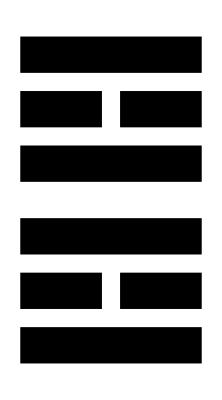

```mathematica
t[y_]:=Graphics@Rectangle[{-5,-1+y},{5,1+y}]
f[y_]:=Graphics[{Rectangle[{-5,-1+y},{-0.5,1+y}],Rectangle[{0.5,-1+y},{5,1+y}]}]
sec[r_]:=Sequence[t[r],f[r+3],t[r+6]]
Show[{sec[10],sec[20]}]
```